```mathematica
ClearAll["Global`*"]
```

## testing

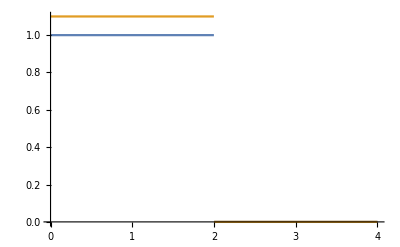

```mathematica
expser=Piecewise[{{1,x<2},{0,x>2}}];
exppar=Piecewise[{{1.1, x<2},{0,x>2}}];
Plot[{expser,exppar},{x,0,4}]
```

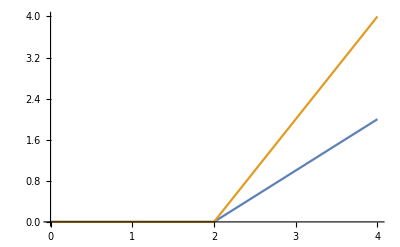

```mathematica
revser=Piecewise[{{0,x<2},{x-2,x>2}}];
revpar=Piecewise[{{0,x<2},{2x-4,x>2}}];
Plot[{revser,revpar},{x,0,4}]
```

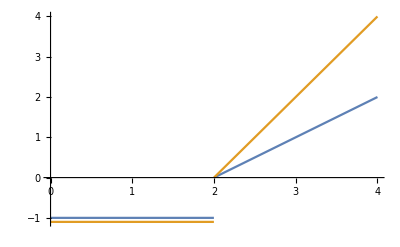

```mathematica
profser=revser-expser;
profpar=revpar-exppar;
Plot[{profser,profpar},{x,0,4}]
```

```mathematica
cashser[x_]=Integrate[profser,x];
cashpar[x_]=Integrate[profpar,x];
```

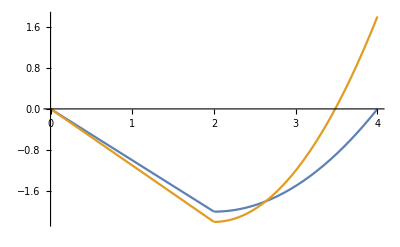

```mathematica
Plot[{cashser[x],cashpar[x]},{x,0,4}]
```

```mathematica
expser
```

Piecewise[{{1, x<2}, {0, True}}]

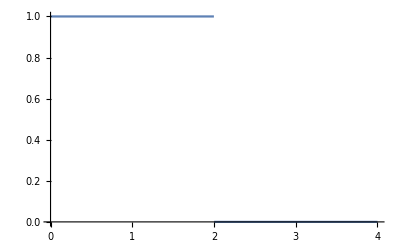

```mathematica
Plot[expser,{x,0,4}]
```

## presentation plot

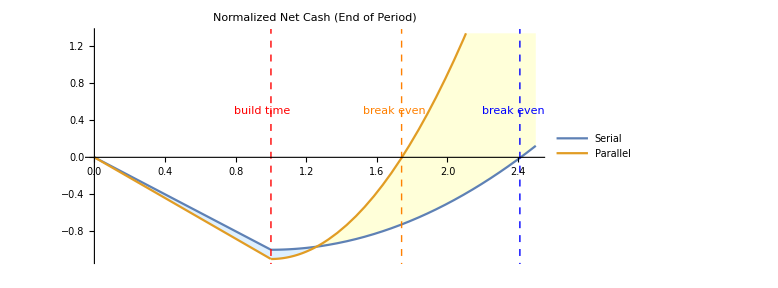

```mathematica
buildtime=1;
increv=4;
expser=Piecewise[{{1,x<buildtime},{0,x>buildtime}}];
exppar=Piecewise[{{1.1, x<buildtime},{0,x>buildtime}}];
revser=Piecewise[{{0,x<buildtime},{x-buildtime,x>buildtime}}];
revpar=Piecewise[{{0,x<buildtime},{increv*x-buildtime*increv,x>buildtime}}];
profser=revser-expser;
profpar=revpar-exppar;
cashser[x_]=Integrate[profser,x];
cashpar[x_]=Integrate[profpar,x];
Show[Plot[{cashser[x],cashpar[x]},{x,0,buildtime*2.5},AspectRatio->.5,Filling->{1->{{2},{LightYellow,LightBlue}}},ImageSize->Large,PlotLegends->{Style["Serial",Large],Style["Parallel",Large]},PlotLabel->Style["Normalized Net Cash (End of Period)",Large]],Graphics[{Dashed,Red,Line[{{1,3},{1,-3}}]}],Graphics[{Dashed,Orange,Line[{{1.74,3},{1.74,-3}}]}],
Graphics[{Dashed,Blue,Line[{{2.41,3},{2.41,-3}}]}],Graphics[Rotate[{Red,Text[Style["build time",Large],{.95,.5}]},270Degree]],Graphics[Rotate[{Orange,Text[Style["break even",Large],{1.7,.5}]},270Degree]],Graphics[Rotate[{Blue,Text[Style["break even",Large],{2.37,.5}]},270Degree]]]
```